```mathematica
(* Test simple Feyn denominator basis for fitting Kyles's chiral B fn *)
```

```mathematica
Λ=0.8;
```

```mathematica
F1=1/(1+q2/Λ^2);F3=F1^3;F3a=(q2/Λ^2)*F3;F5=F1^5;F5a=(q2/Λ^2)^2*F5;
```

```mathematica
FitForm = a1*F1+a3*F3+a3a*F3a+a5*F5+a5a*F5a
```

a5/(1+1.5625 q2)^5+(2.44141 a5a q2^2)/(1+1.5625 q2)^5+a3/(1+1.5625 q2)^3+(1.5625 a3a q2)/(1+1.5625 q2)^3+a1/(1+1.5625 q2)

```mathematica
(* ************Data to be fit******************************* *)
```

```mathematica
B0data=ReadList["/Users/tandy/Dropbox/Peter/Mathematica/Kyle_Bednar_BSE_soln_Nakanishi/b_p_Q_ch11_DSE-ccpQCKernel.txt",{Number,Number}];
```

```mathematica
maxpts=Length[B0data]
```

200

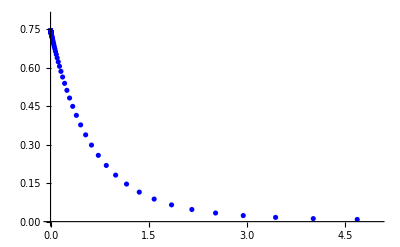

```mathematica
ListPlot[B0data,PlotRange->{{0,5},{-0.001,0.8}},PlotStyle->{Blue}]
```

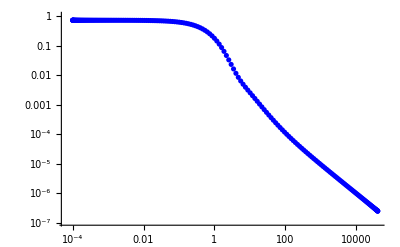

```mathematica
ListLogLogPlot[{B0data},PlotStyle->{Blue}]
```

```mathematica
(* ******************Fit  ********************** *)
```

```mathematica
(* Try FindMinimum of chi rel to max error band -- omit far UV *)
```

```mathematica
chi=(Sum[((B0data[[i,2]]-FitForm/.{q2-> B0data[[i,1]]})/Max[B0data[[i,2]],10^-5 ])^2,{i,1,maxpts}]/maxpts)^0.5;
```

```mathematica
ans=FindMinimum[chi,{a1,a3,a3a,a5,a5a},AccuracyGoal->3]
```

{0.0502531,{a1→0.0149161,a3→1.6066,a3a→0.308811,a5→-0.882787,a5a→1.45363}}

```mathematica
Pars=ans[[2]]
```

{a1→0.0149161,a3→1.6066,a3a→0.308811,a5→-0.882787,a5a→1.45363}

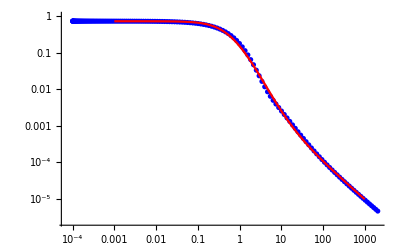

```mathematica
Show[ListLogLogPlot[B0data[[;;150]],PlotStyle->{Blue}],LogLogPlot[FitForm/.Pars,{q2,10^-3,10^3},PlotStyle->RGBColor[1,0,0]]]
```

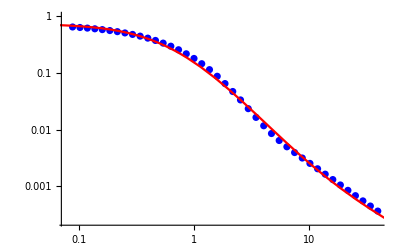

```mathematica
Show[ListLogLogPlot[B0data[[80;;120]],PlotStyle->{Blue}],LogLogPlot[FitForm/.Pars,{q2,10^-3,10^3},PlotStyle->RGBColor[1,0,0]]]
```

```mathematica
(* Now for matrix A---ie the lin combos of basis from discrete k^2 fixes of LHS of BSE *)
```

```mathematica
FitForm/.{q2->0}
```

0.+1. a1+1. a3+1. a5

```mathematica
FitForm/.{q2->(Λ/4)^2}
```

0.941176 a1+0.833706 a3+0.0521067 a3a+0.738508 a5+0.0028848 a5a

```mathematica
FitForm/.{q2->(Λ/2)^2}
```

0.8 a1+0.512 a3+0.128 a3a+0.32768 a5+0.02048 a5a

```mathematica
FitForm/.{q2->(Λ)^2}
```

0.5 a1+0.125 a3+0.125 a3a+0.03125 a5+0.03125 a5a

```mathematica
FitForm/.{q2->(1.25*Λ)^2}
```

0.390244 a1+0.0594304 a3+0.0928599 a3a+0.00905067 a5+0.0220964 a5a

```mathematica
FitForm/.{q2->(1.5*Λ)^2}
```

0.307692 a1+0.0291306 a3+0.0655439 a3a+0.00275793 a5+0.013962 a5a

```mathematica
FitForm/.{q2->(1.75*Λ)^2}
```

0.246154 a1+0.0149149 a3+0.0456768 a3a+0.000903718 a5+0.00847589 a5a

```mathematica
Nq2=5; q2TAB={0,(Λ/4)^2,(Λ/2)^2,(Λ)^2,(1.25*Λ)^2}
```

{0,0.04,0.16,0.64,1.}

```mathematica
(* *** better to rename F1, F3, etc as members of an array **** *)
```

```mathematica
Fbasis={F1,F3,F3a,F5,F5a}
```

{1/(1+1.5625 q2),1/(1+1.5625 q2)^3,(1.5625 q2)/(1+1.5625 q2)^3,1/(1+1.5625 q2)^5,(2.44141 q2^2)/(1+1.5625 q2)^5}

```mathematica
Fbasis[[3]]/.{q2->q2TAB[[2]]}
```

0.0521067

```mathematica
Amat[i_,j_]:= Fbasis[[j]]/.{q2->q2TAB[[i]]}
```

```mathematica
Amatrix=Array[Amat,{Nq2,Nq2}];MatrixForm[Amatrix]
```

(1. | 1. | 0. | 1. | 0.
0.941176 | 0.833706 | 0.0521067 | 0.738508 | 0.0028848
0.8 | 0.512 | 0.128 | 0.32768 | 0.02048
0.5 | 0.125 | 0.125 | 0.03125 | 0.03125
0.390244 | 0.0594304 | 0.0928599 | 0.00905067 | 0.0220964)

```mathematica
Ainv=Inverse[Amatrix];MatrixForm[Ainv]
```

(40.96 | -82.1677 | 66.1376 | -80.9086 | 63.8537
48.06 | -99.4999 | 83.5762 | -74.8642 | 41.4052
-281.6 | 559.767 | -438.161 | 475.338 | -339.223
-88.02 | 181.668 | -149.714 | 155.773 | -105.259
366.82 | -708.054 | 509.853 | -431.131 | 274.87)

```mathematica
(* To multiply:  Ainv.Kmatrix   *)
```